## Math 2325 Project 3 (Chapter 9) - Parametric Curve Representation

Art Duval, Department of Mathematical Sciences, UTEP, El Paso TX 79968
artduval@math.utep.edu
2/13/2005, last edits 2/16/2009.
Modifications by Helmut Knaust, hknaust@utep.edu, 10/10/2012. Last edits 10/18/2021.
Animation originally inspired by Tamara Olson, Michigan Technological University, 2006

## Static Plots

### General Plot

The following shows how to draw general parametric plots, with comments briefly explaining each piece of the command.

```mathematica
ParametricPlot[
{t,Sin[t]},                                       (*x-function, y-function*)
{t,0,2*Pi},                                                (*parameter and its range*)
PlotRange ->{{-2,2},{-2,2}},        (*limits of graphing window*)

AspectRatio->1,PlotPoints->1000,PlotStyle->Directive[Thick,Black],AxesLabel->{x,y}](*technical stuff*)
```

Here's the same command, without the comments, to make it easier for you to modify and draw your own parametric plots.

```mathematica
ParametricPlot[ {Cos[t],Sin[t]},{t,0,2*Pi},PlotRange ->{{-2,2},{-2,2}}, AspectRatio->1,PlotPoints->1000,PlotStyle->Directive[Thick,Black],AxesLabel->{x,y}]
```

### Shortcut: Param2

Param2, below, will make it easy for us to investigate the curves described in Section 9.2.3, namely, the parametric curves x=sin(p t)+cos(q t), y=sin(r t)+cos(s t) over the interval 0≤ t ≤2π.   Note that you must define it before running it!

```mathematica
Param2[p_,q_,r_,s_]:=ParametricPlot[{Sin[p*t]+Cos[q*t],Sin[r*t]+Cos[s*t]},{t,0,2*Pi},PlotRange->{{-2,2},{-2,2}},AspectRatio->1, PlotPoints ->1000,PlotStyle->Directive[Thick,Black],AxesLabel->{x,y}];
```

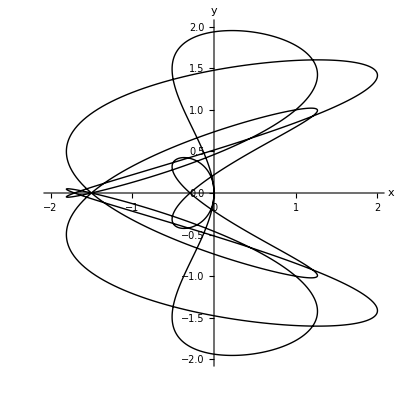

```mathematica
Param2[6,8,5,1]
```

## Animation

The following command will animate a parametric plot.  You can modify: the x-function; the y-function; the interval for the parameter; and the range of the graphing window.

```mathematica
Clear[x,y,t,starttime, endtime,win];
x[t_]=Cos[3t]+Sin[6t];
y[t_]=Sin[4t]+Cos[t];
starttime=0;
endtime=2*Pi;
win=2;

(*Do not change anything below this line*)
Animate[Show[
ParametricPlot[{x[u],y[u]},{u,starttime,endtime}, PlotRange -> {{-win,win},{-win,win}},PerformanceGoal->"Quality",AxesLabel->{x,y}],
ParametricPlot[{x[u],y[u]},{u,starttime,t}, PlotRange -> {{-win,win},{-win,win}},PerformanceGoal->"Quality",
PlotStyle->Directive[Thick,Black]],Graphics[{Red,Thickness[.01],Circle[{x[t],y[t]},.02]}],
Graphics[Text[StringJoin["t = ",ToString[NumberForm[t/Pi,{2,1}]],ToString[Pi,StandardForm]],{.75win,.95win}]]],
{t,starttime+(endtime-starttime)/10.^5,endtime},AnimationRepetitions->1,AppearanceElements->"ResetButton",ControlPlacement->Bottom]
```

To change the size of the graphing window, click on the graph (until you get a yellow box), grab a corner, and resize it.

Here is a shorter version for animations - you can only change p,q,r and s to graph x=sin(p t)+cos(q t), y=sin(r t)+cos(s t) over the interval 0≤ t ≤2π:

```mathematica
Anima2[p_,q_,r_,s_]:=Module[{},{x[t_],y[t_]}={Sin[p t]+Cos[q t],Sin[r t]+Cos[s t]};Animate[Show[
ParametricPlot[{x[u],y[u]},{u,0,2 π}, PerformanceGoal->"Quality",AxesLabel->{x,y}],
ParametricPlot[{x[u],y[u]},{u,0,t}, PerformanceGoal->"Quality",
PlotStyle->Directive[Thick,Black]],Graphics[{Red,Thickness[.01],Circle[{x[t],y[t]},.02]}],
Graphics[Text[StringJoin["t = ",ToString[NumberForm[t/Pi,{2,1}]],ToString[Pi,StandardForm]],{.75win,.95win}]]],
{t,2π/10.^5,2π},AnimationRepetitions->1,AppearanceElements->"ResetButton",ControlPlacement->Bottom]]
```

```mathematica
Anima2[6,8,5,1]
```

## Polar Coordinates

The following shows how to draw general polar coordinate plots, with comments briefly explaining each piece of the command.

```mathematica
r[t_]=Cos[3t];                                        (* the radius r(t) as a function of t*)
ParametricPlot[{r[t]Cos[t],r[t]Sin[t]},                                      
{t,0,2*Pi},                                                (*parameter and its range*)
PlotRange ->{{-3,3},{-3,3}},        (*limits of graphing window*)

AspectRatio->1,PlotPoints->1000,PlotStyle->Directive[Thick,Black],AxesLabel->{x,y}](*technical stuff*)
```

Here's the same command, without the comments, to make it easier for you to modify and draw your own polar coordinate plots:

```mathematica
r[t_]=1+2Cos[t];ParametricPlot[{r[t]Cos[t],r[t]Sin[t]},{t,0,2*Pi},PlotRange ->{{-3,3},{-3,3}},AspectRatio->1,PlotPoints->1000,PlotStyle->Directive[Thick,Black],AxesLabel->{x,y}]
```

Here is the corresponding animation:

```mathematica
Clear[r,x,y,t,starttime, endtime,win];
r[t_]=1+2Cos[t];
starttime=0;
endtime=2*Pi;
win=4;

(*Do not change anything below this line*)
x[t_]=r[t]Cos[t];y[t_]=r[t]Sin[t];
Animate[Show[
ParametricPlot[{x[u],y[u]},{u,starttime,endtime}, PlotRange -> {{-win,win},{-win,win}},AxesLabel->{x,y},PerformanceGoal->"Quality"],
ParametricPlot[{x[u],y[u]},{u,starttime,t}, PlotRange -> {{-win,win},{-win,win}},PerformanceGoal->"Quality",
PlotStyle->Directive[Thick,Black]],Graphics[{Dotted,Gray,Line[{{0,0},{x[t],y[t]}}]}],Graphics[{Red,Thickness[.01],Circle[{x[t],y[t]},.02]}],
Graphics[Text[StringJoin["t = ",ToString[NumberForm[t/Pi,{2,1}]],ToString[Pi,StandardForm]],{.75win,.95win}]]],
{t,starttime+(endtime-starttime)/10.^5,endtime},AnimationRepetitions->1,AppearanceElements->"ResetButton"]
```